```mathematica
ep=0.08;β=0.8;γ=0.5;xmin=-50;xmax=50;maxtime=100; dd1=0.5;dd2=0.001;δ=7.5;
eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

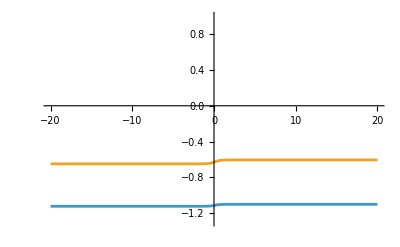

```mathematica
(*Step 1: Starting from the equilibrium, lead to an ok initial guess*)
(*d2=1.5;d1=1;
ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*no block*)*)
ρ1=0.3;slope=2;
ρ[x_]=Which[x<0,0,x<ρ1/slope,x * slope,True,ρ1];
eqn1=FindRoot[(1-ρ1^2/2)v-v^3/3-(v+β)/γ,{v,-1}];
{v1,w1}={v,(v+β)/γ}/.eqn1;

{V1,W1}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==Which[x<0,v0,True,v1], 
u[t, xmin] == v0, 
u[t, xmax] == v1, w[0, x] ==Which[x<0,w0,True,w1], w[t, xmin] == w0,w[t, xmax] == w1}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
{V2,W2}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==V1[maxtime,x], 
u[t, xmin] == v0, 
u[t, xmax] == v1, w[0, x] ==W1[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w1}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{V2[maxtime,x],W2[maxtime,x]},{x,-20,20},PlotRange->{-1.3,1}]
```

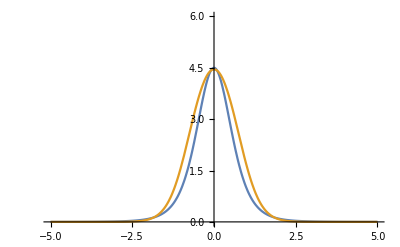

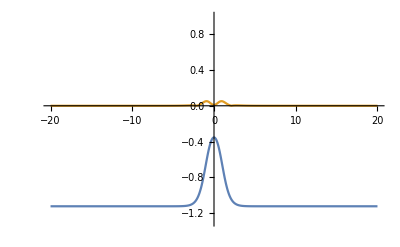

```mathematica
(*Step 3: First approximation to autonomus solution, uses previous iteration*)
{V3,W3}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-δ (V2[maxtime,x]-v0)^2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2  D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==  V2[maxtime,x] +Which[Abs[x+45] <=1, 3, True, 0], 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] == W2[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{ρ[x]^2/2,δ(V3[maxtime,x]-v0)^2},{x,-5,5},PlotRange->{0,6}]
Plot[{V3[maxtime,x],Abs[V3[maxtime,x]-V2[maxtime,x]]},{x,-20,20},PlotRange->{-1.3,1}]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

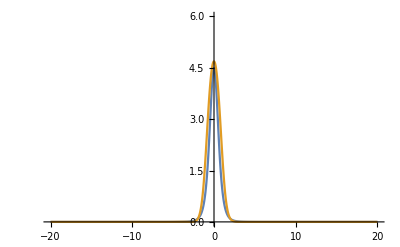

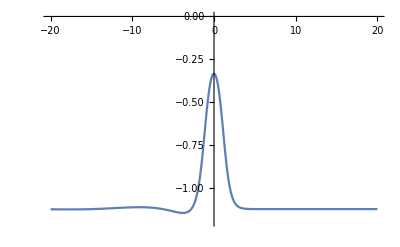

-Graphics3D-

```mathematica
(*Step 4: Test With a traveling pulse*)
{V4,W4}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-δ (V3[t,x]-v0)^2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==  V3[maxtime,x] +Which[Abs[x+45] <=1, 3, True, 0],
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] == W3[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{ρ[x]^2/2,δ(V4[maxtime,x]-v0)^2},{x,-20,20},PlotRange->{0,6}]
Plot[{V4[maxtime,x],Abs[V4[maxtime,x]-V3[maxtime,x]]},{x,-20,20},PlotRange->{-1.2,0}]
Plot3D[V4[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

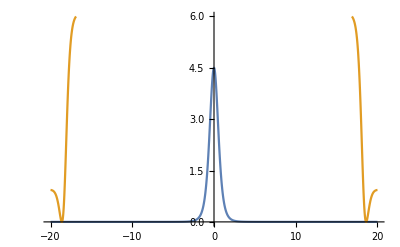

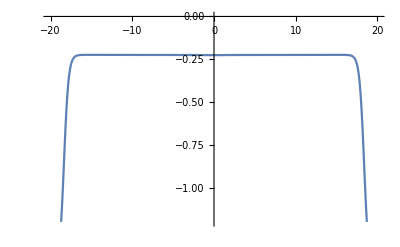

-Graphics3D-

```mathematica
(*Step 4: Test With a traveling pulse*)
dd1=0.5;
{V5,W5}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-δ (u[t,x]-v0)^2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==  V3[maxtime,x], (*+Which[Abs[x+45] <=1, 3, True, 0]*)
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] == W3[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{ρ[x]^2/2,δ(V5[maxtime,x]-v0)^2},{x,-20,20},PlotRange->{0,6}]
Plot[{V5[maxtime,x],Abs[V5[maxtime,x]-V3[maxtime,x]]},{x,-20,20},PlotRange->{-1.2,0}]
Plot3D[V5[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

NDSolveValue::ndsz: At x == 7.93832, step size is effectively zero; singularity or stiff system suspected.

Set::shape: Lists {V4,W4} and NDSolveValue[{-u''[x]==u[x]-u[x]^3/3-w[x],-w''[x]==0.08 (0.8+u[x]-0.5 w[x]),u'[0]==0,w'[0]==0,u[0]==-0.2,w[50]==-0.650345},{u,w},{x,0,50}] are not the same shape.

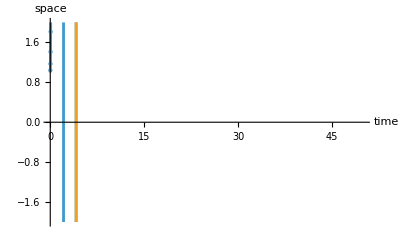

```mathematica
(*(*Step 4b: Solving the Neumann Problem*)
dd1=1;dd2=1;δ=0;
{V4,W4}=NDSolveValue[{- dd1 D[u[ x], x, x]==  u[x](1-δ (u[x]-v0)^2) -u[x]^3/3 - w[x], - dd2 D[w[x], x, x] == ep (u[x] - γ w[x]+β) , 
u'[0]==0,w'[0]==0,u[0] == -0.2, w[xmax] == w0}, {u, w}, {x, 0, xmax}];
Plot[{V4[x],W4[x]}, {x, 0, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]*)
```

```mathematica
.
```

```mathematica
Animate[Plot[{V5[t,x],W5[t,x]},{x,-50,50},PlotRange->{{-60,60},{-2,2}}],{t,0,100},AnimationRunning->False,AnimationRepetitions->1]
```